# Computer Lab 3: Lecture 8

In our computer lab lectures we will work together through concepts and challenges we have discussed over the week in class.  As with your after-class Exercises, you will be expected to turn in your computer lab notebooks before the nect lecture. Please do so by e-mailing your completed *nb file to Lan Yu (ece329.uiuc@gmail.com), make sure you name the file using the following notation: “Exn_Last_First.nb”, where n is the Lecture number (in this case, 8), and First and Last would be your first and last name.  So my submission to Lan for this computer lab would be titled “Ex8_Wasserman_Dan.nb”.  You will receive full credit for your copmputer lab if it turned in before the next lecture (Lecture n+1).  No late submissions will be accepted.

## Objective/Overview:

In class this week we discussed the concept of electrostatic potential.  We now know the relationship between charge and electric field (Gauss’s Law, Coulomb’s Law) and the relationship between electric field and the electrostatic potential (which is a scalar function that describes the potential energy of a positively charged particle of 1C in an electric field).  Putting these together, we came to Poisson and Laplace’s equations, which relate our electrostatic potential (scalar function) and our charge distribution (scalar function) through the Laplacian operator ∇^2 . 
We also determined that the electric field in a conductor (a material that has a conductivity σ that comes from free charge in the material) cannot sustain an electric field, since when you apply an electric field to the material, these charges move around to cancel out the external field.  This means that all conductors have no electric field on their surface, or inside of the conductor, and that therefore a conductor must be an equipotential, namely, the potential along and inside a conductor is constant.
But what about real-world materials that are not conductors?  We know that they still have a lot of atoms, which have electrons and protons....so there is a lot of charge in these materials, just no net charge, and no free charge.  What happens when we apply an electric field to these materials?
Today we find out!

```mathematica
ClearAll[q,eps0,k]
```

## Modeling an Atom

We can think of an atom as having a heavy nucleus with positively charged protons, having total charge of +Z, and a cloud of electrons, having a total charge of -Z.  These electrons are “bound” to the nucleus, so we can think of them as being attached to the nucleus by a spring. We will treat the electron cloud as a point charge, centered at the nucleus.  If we apply an electric field, the electron cloud will be pulled from the nucleus, effectively separating the negative and positive charge of the atom, as shown in the figure below.
-Graphics-
We should be able to model this using our expressions for the electric field of point charges.

```mathematica
eps0=8.85*10^-12; k=1/(4*Pi*eps0);qe=1.6*10^-19;
```

```mathematica
eq[xo_,yo_,zo_,q_]:=(k*q/((x-xo)^2+(y-yo)^2+(z-zo)^2)^1.5)*{x-xo,y-yo,z-zo}
```

```mathematica
VectorPlot3D[eq[0,0,0,eps0],{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

If our the charge of our electron cloud is -8e, the spring constant is kspring=10^-7 , and the applied electric field is E_ext=4 z^∧V/m, then we can write the seperation between positive and negative charge using Newton’s Law:
F=ma=0=-kspring*d-8e*E_ext
d=-8eE_ext/kspring=

```mathematica
-8*1.6*10^-19*4/10^-7
```

-5.12×10^-11

So we should be able to plot the resulting electric field from the displaced electron cloud:

```mathematica
VectorPlot3D[eq[0,0,0,8*qe]+eq[0,0,-5.12*^-11,-8*qe],{x,-10^-10,10^-10},{y,-10^-10,10^-10},{z,-10^-10,10^-10}]
```

-Graphics3D-

We can get a better picture if we take a 2D vector plot of the field.  Let’s call the field “dipole1”, since a dipole is nothing more than two opposite charges displaced from one another by some distance.  The vector field in the xz plane will be called dipole1xz

```mathematica
Clear[dipole1]
```

```mathematica
dipole1=eq[0,0,0,8*qe]+eq[0,0,-5.12*^-11,-8*qe]
```

{(1.15095×10^-8 x)/((x^2+y^2+z^2)^1.5)-(1.15095×10^-8 x)/((x^2+y^2+(5.12×10^-11+z)^2)^1.5),(1.15095×10^-8 y)/((x^2+y^2+z^2)^1.5)-(1.15095×10^-8 y)/((x^2+y^2+(5.12×10^-11+z)^2)^1.5),(1.15095×10^-8 z)/((x^2+y^2+z^2)^1.5)-(1.15095×10^-8 (5.12×10^-11+z))/((x^2+y^2+(5.12×10^-11+z)^2)^1.5)}

```mathematica
dipole1xz={(1.1509510008905428*^-8 x)/((x^2+z^2)^1.5)-(1.1509510008905428*^-8 x)/((x^2+(5.12*^-11+z)^2)^1.5),(1.1509510008905428*^-8 z)/((x^2+z^2)^1.5)-(1.1509510008905428*^-8 (5.12*^-11+z))/((x^2+(5.12*^-11+z)^2)^1.5)}
```

{(1.15095×10^-8 x)/((x^2+z^2)^1.5)-(1.15095×10^-8 x)/((x^2+(5.12×10^-11+z)^2)^1.5),(1.15095×10^-8 z)/((x^2+z^2)^1.5)-(1.15095×10^-8 (5.12×10^-11+z))/((x^2+(5.12×10^-11+z)^2)^1.5)}

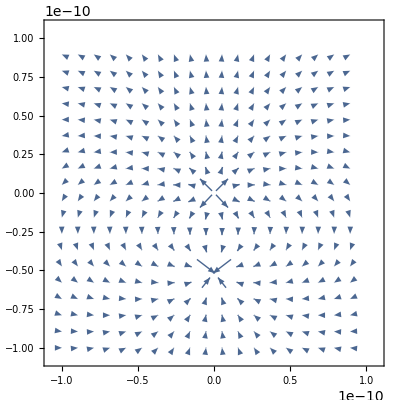

```mathematica
VectorPlot[dipole1xz,{x,-10^-10,10^-10},{z,-10^-10,10^-10}, VectorPoints->20]
```

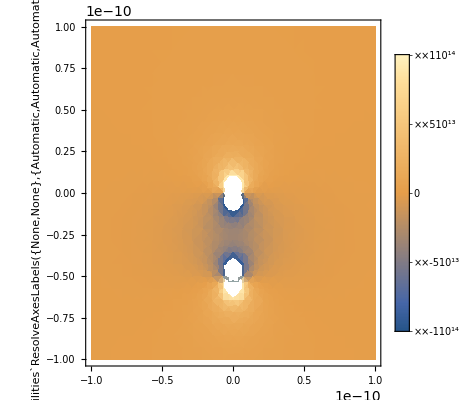

```mathematica
DensityPlot[dipole1xz[[2]],{x,-10^-10,10^-10},{z,-10^-10,10^-10}, PlotRange->{-10^14,10^14}, PlotLegends->Automatic]
```

We see that the relatively small applied electric field produces a very strong electric field (in the opposite direction) in the space between the charges.  But this space is tiny tiny tiny...What we want to do is figure out the average electric field in the material, effectively determining how these dipoles decrease the total field...
In order to calculate the field in an actual material, however, we cannot add up all of the dipoles from all of the atoms....this would mean calculating the fields from 10^22 atoms for a cubic centimeter of material!!  SO how do we handle this?  The figure below gives us some idea

## Modeling an Actual Material

-Graphics-
We can treat the material as a crystal, and each each layer of electrons or protons, at a given z-position, we can treat as a surface charge density ρ_s=±Ke/ΔxΔy.  We know what the field looks like from a surface charge density!  With no external electric field, all of our surface charge densities overlap and cancel out.  But when we apply an electric field, we pull the electrons away from the nuclei, and we separate our surface charges. If our Δx=Δy=Δz=3×10^-10 m=3Å, Z=8, and kspring=10^-7, then our ρ_s=±Zqe/ΔxΔy

```mathematica
rhosheet1=8*qe/(9*10^-20)
```

14.2222

If we calculate the electric field between the separated surface charge densities, we see that we would get a field of E_1=-ρ_s/ϵ_o~-1.5×10^12 V/m!!!  This is huge, and totally unrealistic...in order to get to reasonable values of electric field, we probably should adjust our model significantly, either increasing the spring constant or decreasing the amount of charge that actually shifts...or both. This will give more reasonable values for the electric field between the charge density sheets.
So let’s adjust our ρ_s and kspring to more closely approximate the small charge shift that we actually get from bound charges in real materials.
Δx=Δy=Δz=3×10^-10 m=3Å, Z=10^-10, and kspring=10^-7

```mathematica
rhosheet2=10^-10*qe/(9*10^-20)
```

1.77778×10^-10

```mathematica
e1=-rhosheet2/eps0
```

-20.0879

We can find the seperation between sheets as we did for the dipole:
F=ma=0=-kspring*d-Ze*E_ext
d=-ZeE_ext/kspring=

```mathematica
d=-10^-10*1.6*10^-19*4/(2*10^-18)
```

-3.2×10^-11

And we know that the separation between successive layers of our crystal is

```mathematica
dz=3*10^-10
```

3/10000000000

So the electric field from each of our separated charge layers

```mathematica
esheet[zo_,rho_]:=Piecewise[{{{0,-rho/(2*eps0)},z<zo},{{0,rho/(2*eps0)},z>zo}}]
```

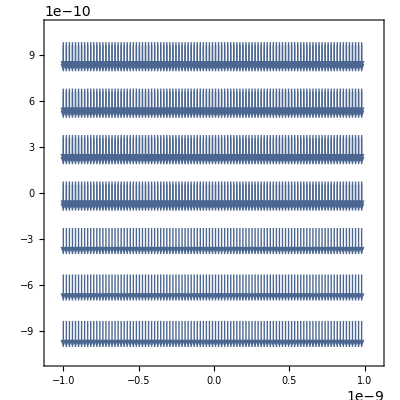

```mathematica
VectorPlot[Sum[esheet[i*dz,rhosheet2]+esheet[i*dz+d,-rhosheet2],{i,-3,3,1}],{x,-1*10^-9,1*10^-9},{z,-1*10^-9,1*10^-9},VectorScale->Small,VectorPoints->100]
```

To find the total electric field, we simply need to add the external electric field to the internal polarization field

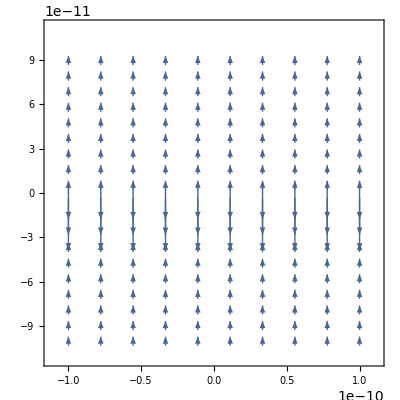

```mathematica
VectorPlot[{0,4}+Sum[esheet[i*dz,rhosheet2]+esheet[i*dz+d,-rhosheet2],{i,-3,3,1}],{x,-.1*10^-9,.1*10^-9},{z,-.1*10^-9,.1*10^-9},VectorScale->Automatic,VectorPoints->{10,20}, PlotLegends->Automatic]
```

We can calculate the average electric field in our system by adding the average polarization field in our material to the external field.
 E1= -ρ_s/ϵ_o=-e/(ΔxΔyϵ_o), OverBar[E_1]=-e/(ΔxΔyϵ_o)(d/Δz)=-ed/(ΔxΔyΔzϵ_o)=edN_d/ϵ_o=-P⃗/ϵ_o

P⃗ is the microscopic Polarization field of the material, and the total Electric Field of the material is now
(E⃗)_tot=(E⃗)_ext-P⃗/ϵ_o

If we take the Divergence of the above expression, we get:
∇·(ϵ_o(E⃗)_tot)=∇·(ϵ_o(E⃗)_ext)-∇·P⃗

We know that the divergence of the external E field should give us the (free) charge distribution responsible for this field (somewhere in the distance):
ρ_tot=ρ_ext-∇·P⃗
We can think of the -∇·P⃗ as the bound charge revealed by the polarization.  If we re-arrange Gauss’s Law: 
∇·(ϵ_o(E⃗)_tot+P⃗)=ρ_free
The term ϵ_o(E⃗)_tot+P⃗ we now re-define to be D⃗=ϵ_o(E⃗)_tot+P⃗, so that ∇·D⃗=ρ_free, which is our same-old Gauss’s Law!!
If the polarization of the medium is linear with the total electric field P⃗=ϵ_o χ_e(E⃗)_tot, where χ_e is the electric susceptibility, then we can write:
 D⃗=ϵ_o(E⃗)_tot+P⃗=ϵ_o(E⃗)_tot+ϵ_o χ_e(E⃗)_tot=ϵ_o(1+χ_e)(E⃗)_tot=ϵ(E⃗)_tot=ϵ_rϵ_o(E⃗)_tot

## Modeling a Polarized Slab

Let’s consider a dielectric slab extending from z=-0.5 to 0.5, infinite in the xy plane, as shown below. If the electric susceptibility of the dielectric is χ_e=3, determine (and plot, when appropriate): ϵ_r, D⃗(x,z), E⃗(x,z), P⃗(x,z),  ρ_ext (free charge) and V(x,z), if the slab is placed between two conducting plates at z=-1, z=1, with surface charge densities ρ_sbottom=2 ϵ_o and ρ_stop=-2 ϵ_o, and V(x,0)=0V.

```mathematica
eps0=8.85*10^-12;
```

```mathematica
χe=3;
```

```mathematica
epsr=1+χe;
```

```mathematica
epsz[z_]:=1+χe*HeavisideTheta[z+0.5]-χe*HeavisideTheta[z-0.5]
```

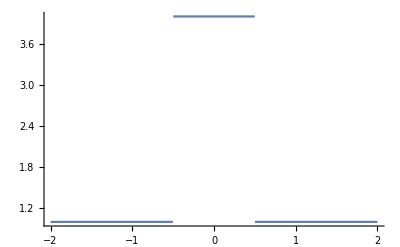

```mathematica
Plot[epsz[z],{z,-2,2}]
```

```mathematica
Clear[eext]
```

```mathematica
eext[z_]:={0,HeavisideTheta[z+1]-HeavisideTheta[z-1]}
```

```mathematica
etot[z_]:=eext[z]/epsz[z]
```

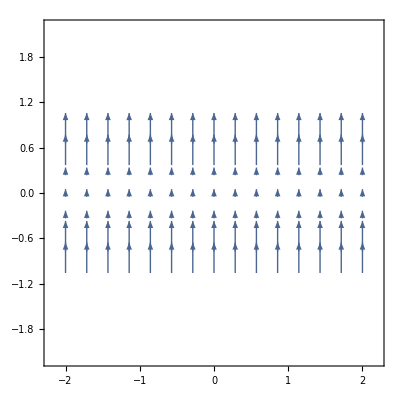

```mathematica
VectorPlot[etot[z],{x,-2,2},{z,-2,2}]
```

```mathematica
dtot[z_]:=etot[z]*epsz[z]
```

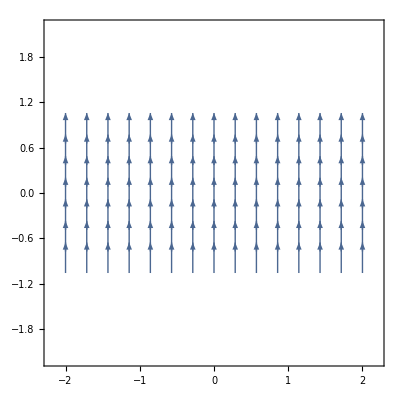

```mathematica
VectorPlot[dtot[z],{x,-2,2},{z,-2,2}]
```

```mathematica
ptot[z_]:=eps0*(epsz[z]-1)*etot[z]
```

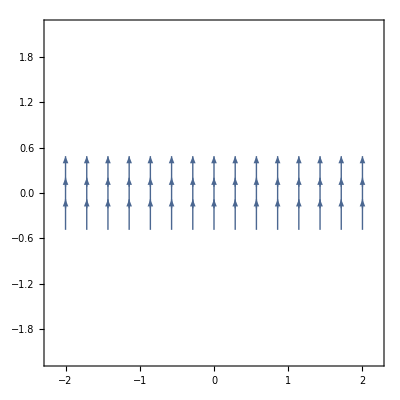

```mathematica
VectorPlot[ptot[z],{x,-2,2},{z,-2,2}]
```

```mathematica
Clear[z]
```

```mathematica
rhotot=Div[dtot[z],{x,z}]
```

-DiracDelta[-1+z]+DiracDelta[1+z]

```mathematica
rhosp=-Div[eps0*epsr*(HeavisideTheta[z+0.5]-HeavisideTheta[z-0.5])*{0,1},{x,z}]
```

-3.54×10^-11 (-DiracDelta[-0.5+z]+DiracDelta[0.5+z])

```mathematica
Clear[epot]
```

```mathematica
epot[z_]:=NIntegrate[etot[zo][[2]],{zo,-1,z}]
```

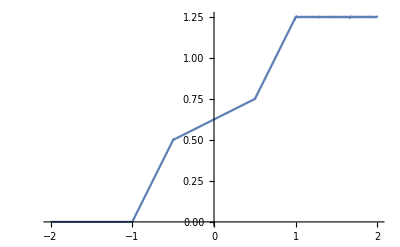

```mathematica
Plot[epot[z],{z,-2,2}]
```